# Ψ_1 proposal (penalizing function)

1/(1+ⅇ^(1/(-1+x)+1/x))

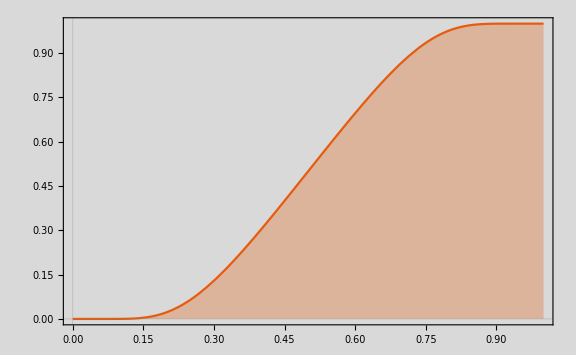

```mathematica
g[x_]=Exp[(-1/x)];
h[x_]=g[x]/(g[x]+g[1-x]) //FullSimplify
Plot[h[x],{x,0,1},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

Piecewise[{{0, x≤0}, {1/(1+ⅇ^(1/(-1+x)+1/x)), 0<x<1}, {1, 1≤x}, {0, True}}]

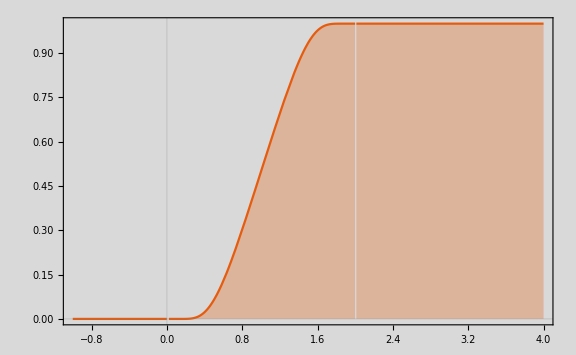

```mathematica
psi1[x_]=Piecewise[{{0,x<=0},{h[x],0<x<1},{1,1<=x}}]
Plot[psi1[.5*x],{x,-1,4},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

```mathematica
psi1'[x]//FullSimplify
```

Piecewise[{{(2+4 (-1+x) x)/(4 (-1+x)^2 x^2 (1+Cosh[1/(-1+x)+1/x])), 0<x<1}, {0, True}}]

```mathematica
psi1''[x]//Expand//FullSimplify
```

Piecewise[{{(ⅇ^(1/(-1+x)+1/x) (-1+2 x-2 x^3 (2+x (-3+2 x))+ⅇ^(1/(-1+x)+1/x) (1-2 (-1+x) x (-3+2 x) (1+(-1+x) x))))/((1+ⅇ^(1/(-1+x)+1/x))^3 (-1+x)^4 x^4), 0<x<1}, {0, True}}]

# Ψ_2 proposal (1): Perona-Malik regularizer (smoothing function)

```mathematica
(*Perona-Malik regularizer*)
Clear[λ];
psi2[x_,λ_] = λ^2 Log[1. + x/λ^2];
Solve[psi2[x,1/40]==1,x];
psi2'[x] //FullSimplify;
psi2''[x] //FullSimplify;
```

λ^2 Log[1.+x/λ^2]

{{x→4.64569894216374×10^691}}

```mathematica
Numerator[-25./(25.+x)^2]
```

-25.

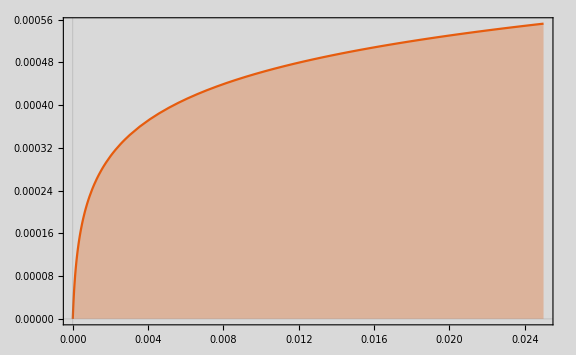

```mathematica
Plot[psi2[x,0.01],{x,0,1/40},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

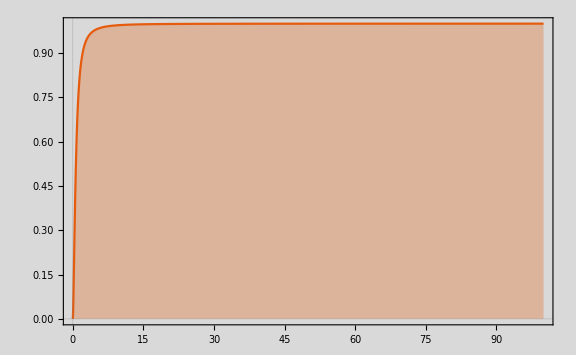

```mathematica
Plot[psi2[1,λ],{λ,0,100},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

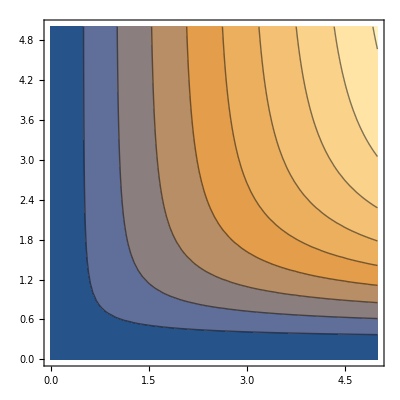

```mathematica
ContourPlot[psi2[x,λ],{x,0,5},{λ,0,5}]
```

# Ψ_2 proposal (2): 5th Order Spline (smoothing function)

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
```

```mathematica
Solve[{f[0]==0, f[1]==1, f'[0]==0, f'[1]==0, f''[0]==0, f''[1]==0},{a,b,c,d,e,f}]
```

{{a→0,b→0,c→0,d→10,e→-15,f→6}}

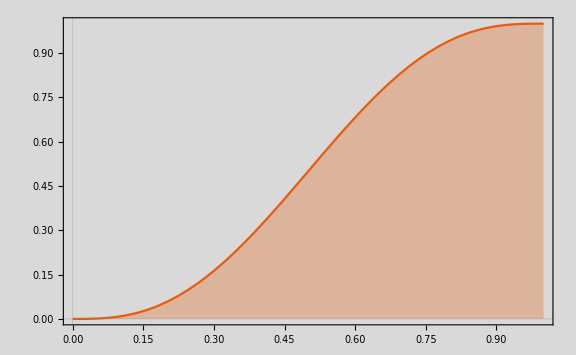

```mathematica
g[x_]= 10*x^3-15*x^4+6*x^5;
Plot[g[x],{x,0,1},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

Piecewise[{{0, x≤0}, {10 x^3-15 x^4+6 x^5, 0<x<1}, {1, 1≤x}, {0, True}}]

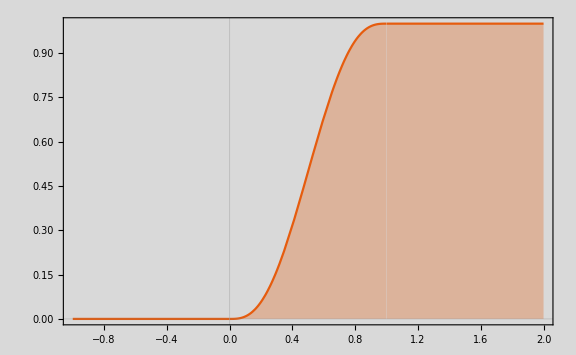

```mathematica
h[x_] =  psi1[x_]=Piecewise[{{0,x<=0},{g[x],0<x<1},{1,1<=x}}]
Plot[h[x],{x,-1,2},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

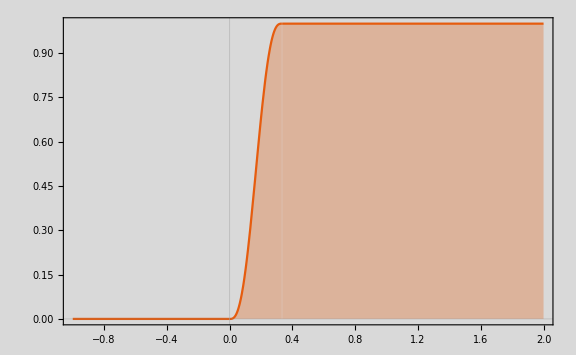

```mathematica
psi2[x_,λ_]=h[λ*x];Plot[psi2[x,3],{x,-1,2},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

```mathematica
(*Derivatives of psi2*)
D[psi2[x,λ],x]
```

Piecewise[{{0, x λ≤0}, {30 x^2 λ^3-60 x^3 λ^4+30 x^4 λ^5, 0<x λ<1}, {0, True}}]

```mathematica
D[psi2[x,λ],{x,2}]
```

Piecewise[{{0, x λ≤0}, {60 x λ^3-180 x^2 λ^4+120 x^3 λ^5, 0<x λ<1}, {0, True}}]